## Sin[x] のTaylor展開

### y = Sin[x] のグラフ

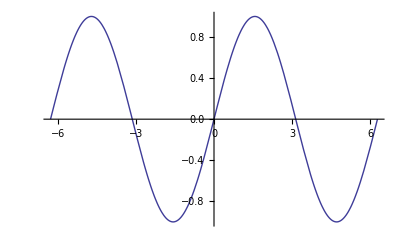

```mathematica
Plot[Sin[x],{x,-2Pi,2Pi}]
```

### Sin[x] を x=0 を中心に5乗の項までテイラー展開

```mathematica
Series[Sin[x],{x,0,5}]
```

x-x^3/6+x^5/120+O[x]^6

```mathematica
Normal[Series[Sin[x],{x,0,5}]]
```

x-x^3/6+x^5/120

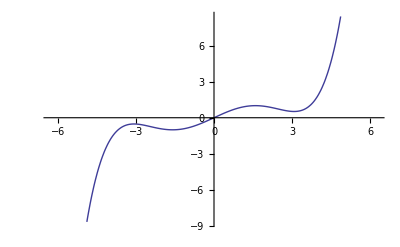

```mathematica
Plot[x-x^3/6+x^5/120,{x,-2Pi,2Pi}]
```

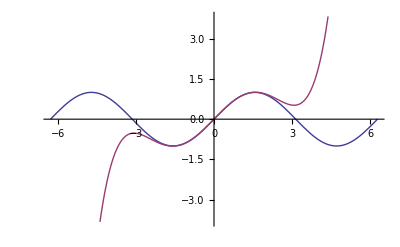

```mathematica
Plot[{Sin[x],x-x^3/6+x^5/120},{x,-2Pi,2Pi}]
```

### y = Sin[x] とテイラー展開した級数とのグラフのちがい

赤色の数値は級数の項の最大次数です．

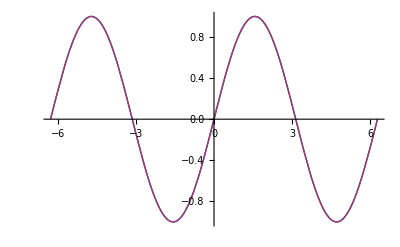

```mathematica
Plot[{Sin[x],Normal[Series[Sin[y],{y,0,20}]]/.y->x},{x,-2Pi,2Pi}]
```

## Log[x] のTaylor展開

### y = Log[x] のグラフ

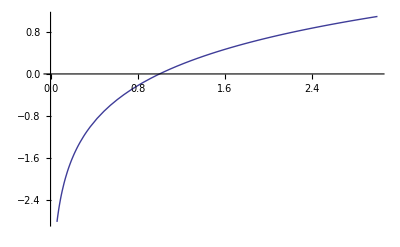

```mathematica
Plot[Log[x],{x,0,3}]
```

### Log[x] を x=1 を中心に5乗の項までテイラー展開

```mathematica
Series[Log[x],{x,1,5}]
```

(x-1)-1/2 (x-1)^2+1/3 (x-1)^3-1/4 (x-1)^4+1/5 (x-1)^5+O[x-1]^6

```mathematica
Normal[Series[Log[x],{x,1,5}]]
```

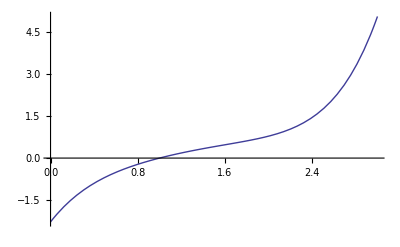

```mathematica
Plot[-1-1/2 (-1+x)^2+1/3 (-1+x)^3-1/4 (-1+x)^4+1/5 (-1+x)^5+x,{x,0,3}]
```

```mathematica
Plot[{Log[x],-1-1/2 (-1+x)^2+1/3 (-1+x)^3-1/4 (-1+x)^4+1/5 (-1+x)^5+x},{x,0.1,3}]
```

### y = Log[x] とテイラー展開した級数とのグラフのちがい

赤色の数値は級数の項の最大次数です．

いくら項数を増やしても，x>2 の範囲で級数は Log[x] には収束しません．

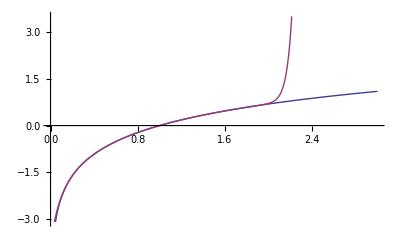

```mathematica
Plot[{Log[x],Normal[Series[Log[y],{y,1,25}]]/.y->x},{x,0,3}]
```